# Vaje za 7. teden

15. 3. in 16. 3. 2023

## Rekurzija in memoizacija

Spodnja funkcija implementira Fibonnacijevo zaporedje.

```mathematica
fib[0] := 0;
fib[1] := 1;
fib[n_] := fib[n-1] + fib[n-2];
```

S pomočjo memoizacije (http://szhorvat.net/pelican/memoization-in-mathematica.html) izračunaj fib[40].

```mathematica
python = 102334155
```

102334155

Naravna števila so v najbolj znani obliki definirana kot {0,1,2,3,4,5,...}, v bolj temeljnih teorijah matematike pa jih poskušamo konstruirati induktivno. Prepoznamo, da je vsako naravno število bodisi 0 bodisi naslednjik nekega naravnega števila (torej bodisi x = 0 ali pa je x naslednjik naravnega števila x - 1). V teoriji množic (eden izmed temeljev matematike) za 0 vzamemo prazno množico {} in funkcijo “naslednjik” definiramo na spodnji način

```mathematica
naslednjik[n_] := {{n}, n};
```

Poišči inverz tej funkciji, torej funkcijo, ki poišče predhodnjik naravnega števila. Pri tem upoštevaj, da nič nima predhodnika, torej bomo posebej definirali

```mathematica
predhodnik[n_] := If[n==0,"nič nima predhodnika",n-1];
```

```mathematica
predhodnik[65]
```

64

```mathematica
predhodnik[0]
```

nič nima predhodnika

Implementiraj funkcijo, ki za dano število n to zapiše v jeziku teorije množic. Npr.

```mathematica
nat2set[0] := {};
nat2set[1] := {{{}}, {}};
```

```mathematica
nat2set[n_]:= naslednjik[nat2set[n-1]]
```

```mathematica
nat2set[3]
```

{{{{{{{}},{}}},{{{}},{}}}},{{{{{}},{}}},{{{}},{}}}}

Implementiraj inverz tej funkciji, torej funkcijo, ki naravno število zapisano v jeziku teorije množic, zapiše kot standardno število, npr.

```mathematica
set2nat[{}] := 0;
```

```mathematica
set2nat[{{n_},n_}]:=1+set2nat[n]
```

```mathematica
set2nat[nat2set[3]]
```

3

## Map funkcija

Implementiraj inverz spodnjih funkcij in pri tem uporabi funkcijo Map (ali skrajšano /@)

```mathematica
Clear[i,j,n,f,g]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
fun0[l_] := Table[5 * l[[i]], {i, 1, Length[l]}];
fun1[l_] := Map[{#, #} &, l];
fun2[l_] := Map[{#, {{#}, #}, {{{#}, #}, #}} &, l];
fun3[{l1_, l2_}] := Table[{l1[[i]],l2[[i]]}, {i, 1, Length[l1]}];
```

{}

```mathematica
fun0inv[l_] := l / 5;
fun1inv[l_] := First /@ l;
fun2inv[l_] := First /@ l;
fun3inv[l_] := {(#[[1]] & /@ l), (#[[2]] & /@ l)};
```

```mathematica
fun3inv[3]
```

{3,3}

```mathematica
fun3[3]
```

```mathematica
fun3[3,3]
```

fun3[3,3]

# Trikotnik

## Osnovne definicije

Trikotnik definiramo kot seznam treh točk. Vsaka točka je seznam (par dveh števil)
Funkcija Stranice vrne seznam parov točk, ki predstavljajo stranice.
Funkcija Koti vrne seznam trojic točk, ki predstavljajo kote.

```mathematica
ClearAll[Stranice, Koti, SlikaOglisc, SlikaStranic]
(* V tej celici so že pripravljene definicije funkcij, ki bodo prišle prav - ni jih treba spreminjati. *)

(* Za trikotnik podan s seznamom točk definiramo funkciji za stranice in kote *)
Stranice[{AA_,BB_,CC_}] :={{BB, CC},{CC, AA}, {AA, BB}}
Koti[{AA_,BB_,CC_}] := {{CC, AA, BB},{AA, BB, CC},{BB, CC, AA}}

(* Definiramo funkciji, ki nam vrneta seznama grafičnih elementov za točke in stranice *)
SlikaOglisc[trikotnik_] := Point[trikotnik]
SlikaStranic[trikotnik_] := Line[Stranice[trikotnik]] 

(* Risanje trikotnika: določimo še barvo, velikost točke, ter debelino črt *)
NarisiTrikotnik[trikotnik_]:=
Graphics[{
GrayLevel[0.7],PointSize[0.02],Thickness[0.005],
SlikaOglisc[trikotnik], 
SlikaStranic[trikotnik]
}]
```

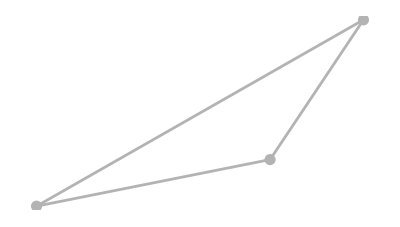

```mathematica
(* Primer uporabe *)
trikotnik={{0,0},{5,1},{7,4}};
NarisiTrikotnik[trikotnik]
```

## Naloga 1

- Posploši zgornje funkcije, da bo za dano število n, rezultat n-kotnik.
- Z uporabo spodnje rotacijske preslikave in ukaza Manipulate, implementiraj slider, ki rotira trikotnik za dani kot phi

```mathematica
rotate[phi_, {x_, y_}] := {x * Cos[phi] - y * Sin[phi], x * Sin[phi] + y * Cos[phi]};
```

```mathematica
Manipulate[NarisiTrikotnik[(rotate[phi,#]&)/@trikotnik],{phi,0,2Pi}]
```

## Simetrale

## Naloga 2

1. Definirajte funkcijo SimetralaKota, ki vrne daljico, ki predstavlja nosilec simetrale kota {a, b, c} z izhodiščem v točki b. Funkcija naj sprejme kot podan s trojico točk in dolžino nosilca, ter vrne koordinati krajišč.
2. Funkcijo definirajte s pomočjo pomožne funkcije VektorSimetraleKota, ki vrne vektor simetrale. Pomagajte si s funkcijo Normalize, ki vrne normaliziran vektor.
3. Naredite grafične objekte za vse tri simetrale kota v trikotniku in jih dodajte v sliko zgoraj. Funkcijo dopolnite tako, da ji dodate opcijski parameter Simetrale, s katerim lahko vklopite ali izklopite risanje simetral (spodaj je enostaven primer). Simetrale narišite bodisi kot vektorje, bodisi kot premice s funkcijo InfiniteLine.

```mathematica
ClearAll[SimetralaKota]
(* 10 je privzeta dolžina vektorja *)
(* Implementaciji seveda nista pravilni, popravite ju. *)
VektorSimetraleKota[{x_,y_,z_}]:=Normalize[x-y]+Normalize[z-y]
SimetralaKota[{x_,y_,z_},dolzina_:10] := {y,y+dolzina*VektorSimetraleKota[{x,y,z}]}

(* Simetrala prvega kota v trikotniku *)
SimetralaKota[First[Koti[trikotnik]]]
```

{{0,0},{10 (5/(√26)+7/(√65)),10 (1/(√26)+4/(√65))}}

Na sliko dorišite še točko, v kateri se sekajo simetrale. Pri reševanju enačbe si pomagajte s funkcijo Solve.
Ta točka je središče včrtane krožnice.

```mathematica
(* Simetrala kota {x,y,z} kot linearna funkcija *)
Simetrala[{x_,y_,z_},t_] :=y+t*VektorSimetraleKota[{x,y,z}]
```

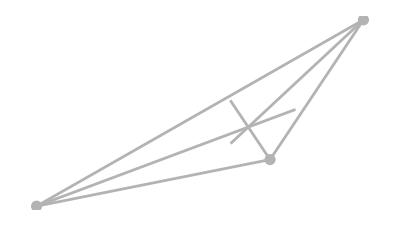

```mathematica
Graphics[{
GrayLevel[0.7],PointSize[0.02],Thickness[0.005],
SlikaOglisc[trikotnik],
SlikaStranic[trikotnik],
Line[SimetralaKota[{trikotnik[[1]], trikotnik[[2]],trikotnik[[3]]},2]],
Line[SimetralaKota[{trikotnik[[2]], trikotnik[[3]],trikotnik[[1]]},2]],
Line[SimetralaKota[{trikotnik[[3]], trikotnik[[1]],trikotnik[[2]]},3]]
}]
```

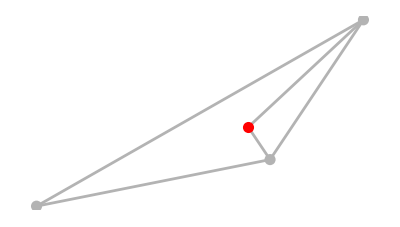

```mathematica
t0 =  t /. Solve[Simetrala[trikotnik, t] == Simetrala[{trikotnik[[2]], trikotnik[[3]], trikotnik[[1]]}, u]];
tocka = Simetrala[trikotnik, t0[[1]]];

Graphics[{
GrayLevel[0.7],PointSize[0.02],Thickness[0.005],
SlikaOglisc[trikotnik], 
SlikaStranic[trikotnik],
Line[SimetralaKota[trikotnik, 1]],
Line[SimetralaKota[{trikotnik[[2]], trikotnik[[3]], trikotnik[[1]]}, 1.7]],
Red,
Point[tocka]
}]
```

## Včrtana krožnica

## Naloga 3

Narišite včrtani krog. Pomagate si lahko s spodnjo funkcijo.

```mathematica
RazdaljaPremicaTocka[{x_, y_}, {a_, b_}, {c_, d_}] := Cross[{x, y, 0} - {a, b, 0}, Normalize[{c, d, 0} - {a, b, 0}]]//Norm
```

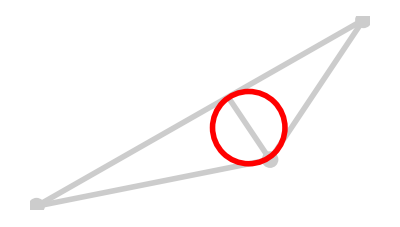

```mathematica
Graphics[{
GrayLevel[0.8],PointSize[0.03],Thickness[0.01],
SlikaOglisc[trikotnik],
SlikaStranic[trikotnik],
Line[SimetralaKota[{trikotnik[[1]], trikotnik[[2]], trikotnik[[3]]},2.1]],
Red,
Circle[tocka,RazdaljaPremicaTocka[tocka,trikotnik[[1]],trikotnik[[2]]]]}]
```